# Superimposed Kerr Metric in Kerr-Schild coordinates.

## Inspiral orbit

### GW150914 trajectory data

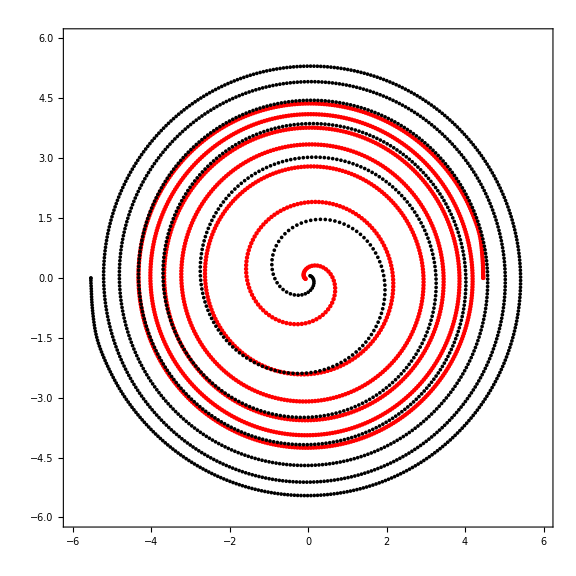

```mathematica
ClearAll[p0,p1];
p0=Import["puncture_0.dat","Table"];
p1=Import["puncture_1.dat","Table"];

ClearAll[drop]
drop=1440;
p0=Drop[p0,-drop];
p1=Drop[p1,-drop];

ClearAll[df];
df=Table[{p0⟦i,1⟧,√((p0⟦i,2⟧-p1⟦i,2⟧)^2+(p0⟦i,3⟧-p1⟦i,3⟧)^2)},{i,1,Length[p0]}];

Show[
ListPlot[p0⟦All,2;;3⟧,PlotRange->{{-6,6},{-6,6}},Axes->False,Frame->True,PlotStyle->Red,ImageSize->Large,AspectRatio->1],
ListPlot[p1⟦All,2;;3⟧,PlotRange->{{-6,6},{-6,6}},Axes->False,Frame->True,PlotStyle->Black]
]
```

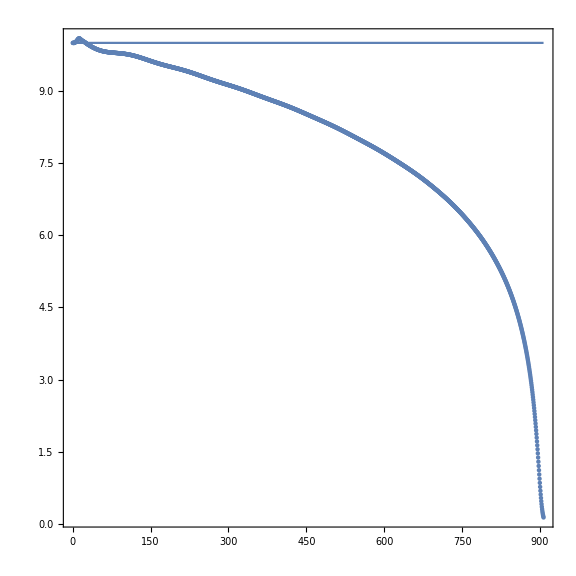

```mathematica
ClearAll[modeldf];
modeldf[t_]=2 √((y0+a[t] Cos[t Ω] Sin[t ω]+b[t] Cos[t ω] Sin[t Ω])^2+(x0+a[t] Cos[t ω] Cos[t Ω]-b[t] Sin[t ω] Sin[t Ω])^2);

ClearAll[x0,y0];
x0=0;
y0=0;

ClearAll[Ω,ω];
Ω=1;
ω=0;

ClearAll[a,b];
a[t_]=1;
b[t_]=1;

Show[
ListPlot[df,PlotRange->Full,AspectRatio->1,Axes->False,Frame->True,ImageSize->Large],
Plot[df⟦1,2⟧,{t,0,p0⟦-1,1⟧},PlotRange->Full,AspectRatio->1,Axes->False,Frame->True,ImageSize->Large],
PlotRange->Full
]

ClearAll[modeldf];
ClearAll[x0,y0];
ClearAll[Ω,ω];
ClearAll[a,b];
```

### General Elipse

```mathematica
ClearAll[r1]
r1[t_]={
x0+a[t]Cos[Ω*t]Cos[ω*t]-b[t]Sin[Ω*t]Sin[ω*t],
y0+a[t]Cos[Ω*t]Sin[ω*t]+b[t]Sin[Ω*t]Cos[ω*t]
};

ClearAll[r2]
r2[t_]={
-x0-a[t]Cos[Ω*t]Cos[ω*t]+b[t]Sin[Ω*t]Sin[ω*t],
-y0-a[t]Cos[Ω*t]Sin[ω*t]-b[t]Sin[Ω*t]Cos[ω*t]
};

ClearAll[d];
d[t_]=FullSimplify[√((r1[t]-r2[t]).(r1[t]-r2[t]))];

ClearAll[e];
e[t_]:=√(1-b[t]^2/a[t]^2);
```

e(t) = 0

d(t) = 0.63661977 √((14.016336-1. t)^2)

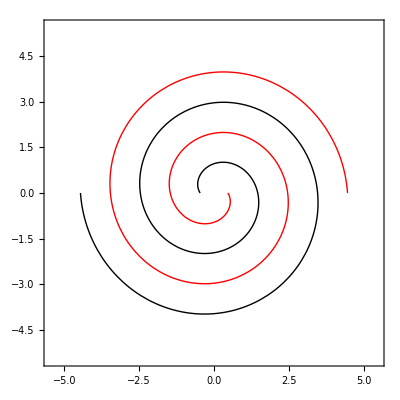

```mathematica
ClearAll[x0,y0];
x0=0;
y0=0;

ClearAll[Ω,ω];
Ω=1;
ω=0;

ClearAll[c];
c=p0⟦1,2⟧;

ClearAll[a,b];
a[t_]=InterpolatingPolynomial[{{0,c},{π/Ω,c-1}},t];
b[t_]=a[t];

ClearAll[tf];
tf=2(2π)/Ω;

Print["e(t) = ",e[t]];
Print["d(t) = ",FullSimplify[d[t]]];
Show[
ParametricPlot[r1[t],{t,0,tf},PlotRange->{{-c-1,c+1},{-c-1,c+1}},AspectRatio->1,PlotStyle->Directive[Red,Thick]],
ParametricPlot[r2[t],{t,0,tf},PlotRange->{{-c-1,c+1},{-c-1,c+1}},AspectRatio->1,PlotStyle->Directive[Black,Thick]],
Axes->False,
Frame->True
]

ClearAll[x0,y0];
ClearAll[Ω,ω];
ClearAll[c];
ClearAll[a,b];
ClearAll[tf];
```

## Assumptions

```mathematica
$Assumptions=M1∈Reals&&M1>0&&M2∈Reals&&M2>0&&b∈Reals&&b>0&&bhIdx∈Integers&&Ω∈Reals&&Ω>0;
```

## Trajectory

```mathematica
ClearAll[s];
s[bhIdx_,1,t_]=(-1)^(bhIdx+1)b/2 Cos[Ω*t];
s[bhIdx_,2,t_]=(-1)^(bhIdx+1)b/2 Sin[Ω*t];
s[bhIdx_,3,t_]=0;
```

## Trajectory Parameters

```mathematica
ClearAll[v,v2];
v[bhIdx_,1]=FullSimplify[D[s[bhIdx,1,t],t]];
v[bhIdx_,2]=FullSimplify[D[s[bhIdx,2,t],t]];
v[bhIdx_,3]=FullSimplify[D[s[bhIdx,3,t],t]];
v2[bhIdx_]=FullSimplify[v[bhIdx,1]^2+v[bhIdx,2]^2+v[bhIdx,3]^2];

ClearAll[n];
n[bhIdx_,1]=FullSimplify[v[bhIdx,1]/√v2[bhIdx]];
n[bhIdx_,2]=FullSimplify[v[bhIdx,2]/√v2[bhIdx]];
n[bhIdx_,3]=FullSimplify[v[bhIdx,3]/√v2[bhIdx]];

ClearAll[γ];
γ=FullSimplify[1/(√(1-v2[bhIdx])),{b>0,M1>0,M2>0,bhIdx∈Integers}];
```

## Lorentz Boost

```mathematica
ClearAll[Λ];
Λ[bhIdx_]=FullSimplify[
{
{γ,-γ*v[bhIdx,1],-γ*v[bhIdx,2],-γ*v[bhIdx,3]},
{-γ*v[bhIdx,1],1+(γ-1)n[bhIdx,1]n[bhIdx,1],(γ-1)n[bhIdx,1]n[bhIdx,2],(γ-1)n[bhIdx,1]n[bhIdx,3]},
{-γ*v[bhIdx,2],(γ-1)n[bhIdx,2]n[bhIdx,1],1+(γ-1)n[bhIdx,2]n[bhIdx,2],(γ-1)n[bhIdx,2]n[bhIdx,3]},
{-γ*v[bhIdx,3],(γ-1)n[bhIdx,3]n[bhIdx,1],(γ-1)n[bhIdx,3]n[bhIdx,2],1+(γ-1)n[bhIdx,3]n[bhIdx,3]}
}
];
```

## Local Coordinates

```mathematica
ClearAll[eqt,eqx,eqy,eqz];
eqt[bhIdx_]=γ(T-(v[bhIdx,1]X+v[bhIdx,2]Y));
eqx[bhIdx_]=s[bhIdx,1,t]+X(1+(γ-1)n[bhIdx,1]n[bhIdx,1])+Y((γ-1)n[bhIdx,1]n[bhIdx,2]);
eqy[bhIdx_]=s[bhIdx,2,t]+X((γ-1)n[bhIdx,1]n[bhIdx,2])+Y(1+(γ-1)n[bhIdx,2]n[bhIdx,2]);
eqz[bhIdx_]=Z;

ClearAll[local2GlobalSystem];
local2GlobalSystem={
eqt[bhIdx]==t,
eqx[bhIdx]==x,
eqy[bhIdx]==y,
eqz[bhIdx]==z
};

ClearAll[sol];
sol=FullSimplify[Flatten[Solve[local2GlobalSystem,{T,X,Y,Z}]]];


ClearAll[eqT,eqX,eqY,eqZ];
eqT[bhIdx_]=T/.sol
eqX[bhIdx_]=X/.sol
eqY[bhIdx_]=Y/.sol
eqZ[bhIdx_]=Z/.sol

ClearAll[sol];
```

1/4 √(4-b^2 Ω^2) (2 t+(-1)^(1+bhIdx) b Ω (y Cos[t Ω]-x Sin[t Ω]))

1/4 (2 (-1)^bhIdx b Cos[t Ω]+4 x Cos[t Ω]^2+2 y Sin[2 t Ω]+√(4-b^2 Ω^2) (2 x Sin[t Ω]^2-y Sin[2 t Ω]))

1/4 (y (2+√(4-b^2 Ω^2))+y (-2+√(4-b^2 Ω^2)) Cos[2 t Ω]+2 (-1)^bhIdx b Sin[t Ω]-x (-2+√(4-b^2 Ω^2)) Sin[2 t Ω])

z

## Single KS metric aux functions

```mathematica
ClearAll[r];
r[a_,X_,Y_,Z_]=FullSimplify[√(1/2(-a^2+X^2+Y^2+Z^2+√(4 a^2 Z^2+(-a^2+X^2+Y^2+Z^2)^2)))];

ClearAll[H];
H[M_,a_,X_,Y_,Z_]=FullSimplify[(2M*r[a,X,Y,Z]^3)/(r[a,X,Y,Z]^4+a^2*Z^2)];

ClearAll[l];
l[a_,X_,Y_,Z_,1]=1;
l[a_,X_,Y_,Z_,2]=FullSimplify[(r[a,X,Y,Z]*X+a*Y)/(r[a,X,Y,Z]^2+a^2)];
l[a_,X_,Y_,Z_,3]=FullSimplify[(r[a,X,Y,Z]*Y-a*X)/(r[a,X,Y,Z]^2+a^2)];
l[a_,X_,Y_,Z_,4]=FullSimplify[Z/r[a,X,Y,Z]];
```

## Boosted ℋ

```mathematica
ClearAll[boostedL];
boostedL[bhIdx_,a_,X_,Y_,Z_,1]=FullSimplify[Λ[bhIdx]⟦1,1⟧l[a,X,Y,Z,1]+Λ[bhIdx]⟦2,1⟧l[a,X,Y,Z,2]+Λ[bhIdx]⟦3,1⟧l[a,X,Y,Z,3]+Λ[bhIdx]⟦4,1⟧l[a,X,Y,Z,4]];
boostedL[bhIdx_,a_,X_,Y_,Z_,2]=FullSimplify[Λ[bhIdx]⟦1,2⟧l[a,X,Y,Z,1]+Λ[bhIdx]⟦2,2⟧l[a,X,Y,Z,2]+Λ[bhIdx]⟦3,2⟧l[a,X,Y,Z,3]+Λ[bhIdx]⟦4,2⟧l[a,X,Y,Z,4]];
boostedL[bhIdx_,a_,X_,Y_,Z_,3]=FullSimplify[Λ[bhIdx]⟦1,3⟧l[a,X,Y,Z,1]+Λ[bhIdx]⟦2,3⟧l[a,X,Y,Z,2]+Λ[bhIdx]⟦3,3⟧l[a,X,Y,Z,3]+Λ[bhIdx]⟦4,3⟧l[a,X,Y,Z,4]];
boostedL[bhIdx_,a_,X_,Y_,Z_,4]=FullSimplify[Λ[bhIdx]⟦1,4⟧l[a,X,Y,Z,1]+Λ[bhIdx]⟦2,4⟧l[a,X,Y,Z,2]+Λ[bhIdx]⟦3,4⟧l[a,X,Y,Z,3]+Λ[bhIdx]⟦4,4⟧l[a,X,Y,Z,4]];

ClearAll[boostedℋ];
boostedℋ[bhIdx_,M_,a_,X_,Y_,Z_,AA_,BB_]=FullSimplify[H[M,a,X,Y,Z]boostedL[bhIdx,a,X,Y,Z,AA]boostedL[bhIdx,a,X,Y,Z,BB]];
```

## 4-metric assembly

```mathematica
ClearAll[llgSKS];
llgSKS=Block[
{η,X1,Y1,Z1,X2,Y2,Z2,bh1,bh2,i,j},

X1=eqX[1];
Y1=eqY[1];
Z1=eqZ[1];

X2=eqX[2];
Y2=eqY[2];
Z2=eqZ[2];

bh1=ConstantArray[0,{4,4}];
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
bh1⟦i,j⟧=(boostedℋ[1,M,a,X,Y,Z,i,j]//.{M->M1,a->a1,X->X1,Y->Y1,Z->Z1});
]
];

bh2=ConstantArray[0,{4,4}];
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
bh2⟦i,j⟧=(boostedℋ[2,M,a,X,Y,Z,i,j]//.{M->M2,a->a2,X->X2,Y->Y2,Z->Z2});
]
];

η=DiagonalMatrix[{-1,1,1,1}];

η+bh1+bh2
];
```

## Save metric

```mathematica
uugSKS=Inverse[llgSKS];
DumpSave["~/llgsks.mx",llgSKS];
DumpSave["~/uugsks.mx",uugSKS];
```